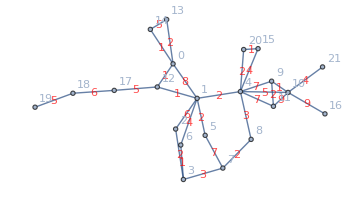

```mathematica
Clear["`*"];
SeedRandom@1;
g=Graph[#,EdgeWeight->RandomInteger[{1,10},EdgeCount@#]]&@Graph[{0<->13,13<->14,14<->0,0<->1,12<->1,0<->12,10<->16,4<->9,9<->10,10<->4,11<->9,11<->10,1<->2,2<->3,1<->4,1<->5,1<->6,4<->8,8<->7,5<->7,6<->3,7<->3,11<->4,12<->17,17<->18,18<->19,4<->15,15<->20,20<->4,10<->21},GraphLayout->"SpringEmbedding",VertexLabels->"Name",EdgeLabels->"EdgeWeight",EdgeLabelStyle->Red,ImageSize->Medium]

pt={1,8,9};


(*g=Graph[{1<->4,1<->6,1<->7,2<->5,2<->8,2<->9,2<->10,3<->6,3<->9,3<->11,4<->6,4<->11,5<->7,7<->10,8<->9,8<->10,8<->11},EdgeWeight->ConstantArray[1,17],GraphLayout->"SpringEmbedding",VertexLabels->"Name",EdgeLabels->"EdgeWeight",EdgeLabelStyle->Red,ImageSize->Medium]
pt={1,2};*)

style={VertexLabels->"Name",EdgeLabels->"EdgeWeight",EdgeLabelStyle->Red,ImageSize->Medium,PlotRange->MinMax/@Transpose[PropertyValue[{g,#},VertexCoordinates]&/@VertexList@g]};
vc[g_]:=VertexCoordinates->(#->PropertyValue[{g,#},VertexCoordinates]&/@VertexList@g);
highstyle[color_,ver_,edge_]:={Style[#,Darker[color,.65]]&/@ver,Style[#,Darker@color,Thick]&/@edge};

delhighlight[g_]:=Fold[SetProperty[{#1,#2},GraphHighlight->False]&,g,PropertyValue[g,GraphHighlight]];

myVertexDelete[g_,ptl_]:=Block[{ea=Association[#->PropertyValue[{g,#},EdgeWeight]&/@EdgeList@g],el},Graph[el=EdgeList@VertexDelete[g,ptl],EdgeWeight->ea/@el,style,VertexCoordinates->(#->PropertyValue[{g,#},VertexCoordinates]&/@Complement[VertexList@g,ptl])]]
```

```mathematica
delline[g_]:=Block[{del=Complement[VertexList@g,DeleteDuplicates@Flatten[FindPath[g,First@pt,#,Infinity,All]&/@Rest@pt]]},{HighlightGraph[g,highstyle[Orange,del,Flatten[Thread[DeleteCases[VertexComponent[g,#,1],#]<->#]&/@del]]],myVertexDelete[g,del]}];

mergep[resl_,cg_:True]:=Block[{prep=#[[1,1]]->1/Total[1/#[[;;,2]]]&/@GatherBy[resl,Sort@#[[1]]&]},Graph[prep[[;;,1]],EdgeWeight->prep[[;;,2]],style,If[cg=!=True,vc@cg,Automatic]]];

mline[g_]:=Block[{vn=VertexList@g,vd=VertexDegree@g,ea=Association@Thread[EdgeList@g->PropertyValue[g,EdgeWeight]],r,subg},r=UndirectedEdge@@Complement[VertexComponent[g,#,1],#]->Total[ea/@EdgeList[g,(Alternatives@@#)<->_]]&/@ConnectedComponents[subg=Subgraph[g,Complement[Pick[vn,vd,2],pt]]];{HighlightGraph[g,highstyle[Green,VertexList@subg,EdgeList[g,(Alternatives@@VertexList@subg)<->_]],style],HighlightGraph[mergep[Join[#->ea@#&/@EdgeList@VertexDelete[g,VertexList@subg],r],g],Style[#,Darker[Green,.65],Thick]&/@DeleteDuplicates[r[[;;,1]]]]}];

simpleproc[g_]:=Most@NestWhileList[mline@*delhighlight@*Last,{g},Unequal@@(Sort@*EdgeList/@#)&];

s2t[r:{r1_,r2_,r3_}]:=(RotateRight[r].r)/r;
t2s[r:{r23_,r13_,r12_}]:=RotateRight@r RotateLeft@r/Total@r

simplifybypoints[g_,center_]:=Block[{adj,ea=Association@Thread[EdgeList@g->PropertyValue[g,EdgeWeight]],newedge},adj=Complement[VertexComponent[g,center,1],{center}];newedge=UndirectedEdge@@@Thread[{RotateRight@adj,RotateLeft@adj}];{HighlightGraph[g,highstyle[Purple,Append[adj,center],Thread[adj<->center]]],HighlightGraph[mergep[Join[#->ea@#&/@EdgeList@VertexDelete[g,center],Thread[newedge->s2t[PropertyValue[{g,UndirectedEdge[#,center]},EdgeWeight]&/@adj]]],g],highstyle[Darker@Purple,adj,newedge]]}];

simplifybycycle[g_,cycle_]:=Block[{newp=Unique["new"],ea=Association@Thread[EdgeList@g->PropertyValue[g,EdgeWeight]],el=EdgeList@EdgeDelete[g,cycle],vl=VertexList@Graph@cycle,newedge},{HighlightGraph[g,highstyle[Purple,vl,cycle]],HighlightGraph[Graph[Join[el,newedge=Thread[newp<->Complement[vl,#][[1]]&/@List@@@cycle]],EdgeWeight->Join[ea/@el,t2s[PropertyValue[{g,#},EdgeWeight]&/@cycle]],style,VertexCoordinates->Append[#->PropertyValue[{g,#},VertexCoordinates]&/@VertexList@g,newp->Mean[PropertyValue[{g,#},VertexCoordinates]&/@vl]]],highstyle[Darker@Purple,{newp},newedge]]}]

complexproc[g_]:=Block[{cycle,center},If[(cycle=FindCycle[Graph@EdgeList@g,{3}])==={},If[(center=SelectFirst[Thread[{VertexList@g,VertexDegree@g}],#[[2]]==3&&FreeQ[pt,#[[1]]]&])==={},{g,g},simplifybypoints[delhighlight@g,center[[1]]]],simplifybycycle[delhighlight@g,cycle[[1]]]]];


allproc[g_]:=TimeConstrained[Grid[Select[Flatten[NestWhileList[Block[{res=simpleproc@#[[-1,-1]],res1},res1=complexproc@res[[-1,-1]];
Join[res,{res1,delline@delhighlight@res1[[-1]]}]]&,{delline@g},!SubsetQ[pt,VertexList@#[[-1,-1]]]&],1],Length@#==2&&!IsomorphicGraphQ[#[[1]],#[[2]]]&],Spacings->{5,5}],600]

dynamicproc[g_]:=TimeConstrained[ListAnimate@Flatten[Select[Flatten[NestWhileList[Block[{res=simpleproc@#[[-1,-1]],res1},res1=complexproc@res[[-1,-1]];
Join[res,{res1,delline@delhighlight@res1[[-1]]}]]&,{delline@g},!SubsetQ[pt,VertexList@#[[-1,-1]]]&],1],Length@#==2&&!IsomorphicGraphQ[#[[1]],#[[2]]]&],1],600]
```

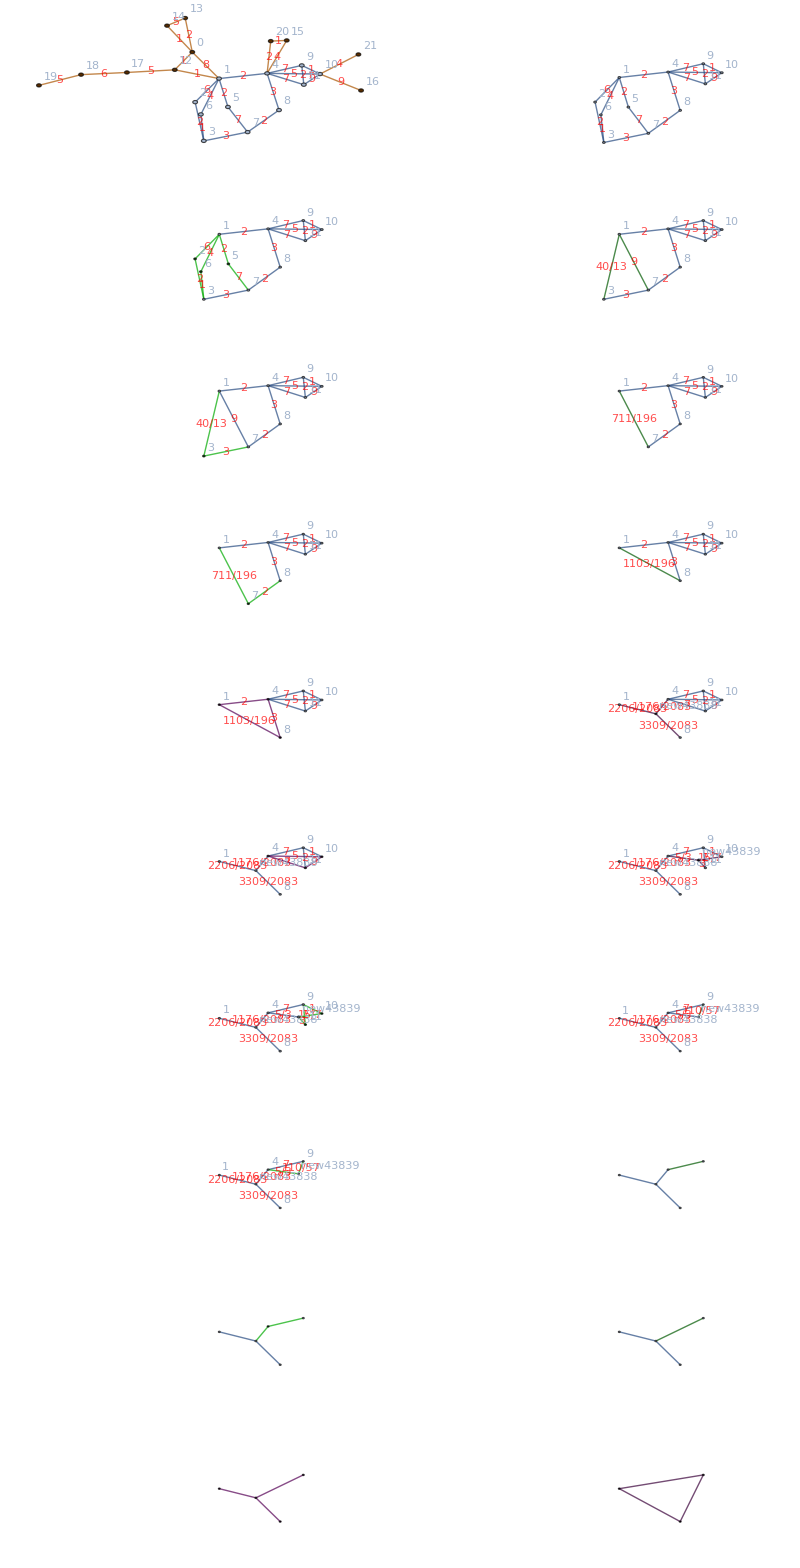

```mathematica
allproc@g
```